```mathematica
zn = Cos[ts];
Lz = 1/2 Cos[tl] - (√3)/2(Sin[tl] Cos[p0 - pl]);
Ln = Cos[tl] Cos[ts] + Sin[tl]Sin[ts]Cos[pl - ps];
nLz = 1/2 Sin[tl]Sin[ts]Sin[pl-ps] - (√3)/2 Cos[p0](Cos[tl]Sin[ts]Sin[ps] - Cos[ts]Sin[tl] Sin[pl]) - (√3)/2 Sin[p0](Cos[ts]Sin[tl] Cos[pl] - Cos[tl]Sin[ts]Cos[ps]);
```

```mathematica
eq1 = {Tan[psi] == (Lz - Ln zn)/nLz}
```

{Tan[psi]==(Cos[tl]/2-1/2 √3 Cos[p0-pl] Sin[tl]-Cos[ts] (Cos[tl] Cos[ts]+Cos[pl-ps] Sin[tl] Sin[ts]))/(1/2 Sin[pl-ps] Sin[tl] Sin[ts]-1/2 √3 Sin[p0] (Cos[pl] Cos[ts] Sin[tl]-Cos[ps] Cos[tl] Sin[ts])-1/2 √3 Cos[p0] (-Cos[ts] Sin[pl] Sin[tl]+Cos[tl] Sin[ps] Sin[ts]))}

```mathematica
Solve[Tan[psi] == (Lz - Ln zn)/nLz,pl]
```

$Aborted

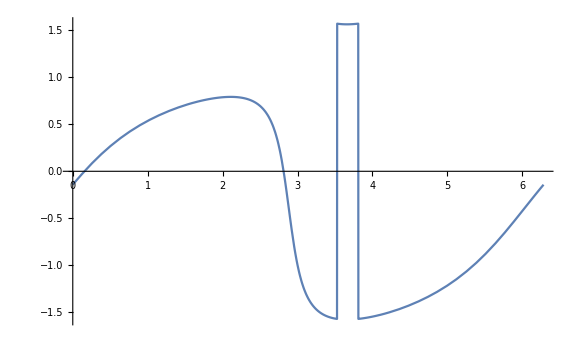

```mathematica
Plot[ArcTan[(Lz - Ln zn)/nLz]/.ts->1.1/.ps->3/.tl->1/.p0->1,{pl,0,2π},PlotRange->Automatic,ImageSize->Large]
```